```mathematica
Clear@u;
input=11;
nNvec⟦input⟧
ν
aS=1;
```

9

3

```mathematica
h[u]=Sum[   wMatrix⟦aS,aQ⟧  Chop[Sum[bInMatrix[[aQ,xk+1,input]]u^(xk),{xk,0,Length[bMatrix]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify
h'[u]=D[h[u],{u,1}]
h''[u]=D[h[u],{u,2}]
hp2[u]=Sum[   wMatrix⟦aS,aQ⟧  Chop[Sum[bInMatrix[[aQ,xk+1,input+1]]u^(xk),{xk,0,Length[bMatrix]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify
hm2[u]=Sum[   wMatrix⟦aS,aQ⟧  Chop[Sum[bInMatrix[[aQ,xk+1,input-1]]u^(xk),{xk,0,Length[bMatrix]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify
```

8.70932×10^-18+u (-7.81397×10^-18+u (-3.64652×10^-17+u (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))))))

-7.81397×10^-18+u (-3.64652×10^-17+u (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))))))+u (-3.64652×10^-17+u (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))))+u (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))))+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)+u (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u))))))

u (u (u (u (u ((2 (1.02392+0.230944 u)+0.230944 u) u+2 (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u))+2 (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)+u (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u)))+2 (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)+u (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u))))+2 (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)+u (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u)))))+2 (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))))+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)+u (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u))))))+2 (-3.64652×10^-17+u (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))))+u (8.12653×10^-16+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))))+u (-4.5842×10^-16+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)))+u (0.484006+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u))+u (-0.481086+u (-1.06803+(1.02392+0.115472 u) u)+u (-1.06803+(1.02392+0.115472 u) u+(1.02392+0.230944 u) u))))))

6.92779×10^-18+u (-2.11133×10^-17-1.31958×10^-16 u+7.91747×10^-16 u^3+0.188622 u^4-0.221908 u^5-0.425324 u^6+0.501435 u^7)

-7.47326×10^-18+u (-5.3036×10^-18+u (-2.77716×10^-16+u (1.94401×10^-15+u (-7.40576×10^-16+u (-0.0992425+u (0.273728+u (1.10096+u (-1.63674+u (-1.6815+2.1189 u)))))))))

```mathematica
Clear@n
f[u] = (1+u)^((ν+n)/4) (1-u)^((n-ν)/4) w[u];
FullSimplify[(-4/u) FullSimplify[D[FullSimplify[u*(1-u^2)D[f[u],{u,1}]],{u,1}]]]
```

-1/u(1-u)^(1/4 (-7+n)) (1+u)^(1/4 (-1+n)) ((6+u (9-4 n-6 (1+n) u+n (4+n) u^2)) w[u]+4 (-1+u^2) ((-1+u (-3+(3+n) u)) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[% +(f[u]/(1-u^2))*(ν^2+n^2-2ν n u) +(4f[u]/u^2)(1/2)(j(j+1)-n^2)-f[u]*k(k+4)]
```

1/u^2(1-u)^(1/4 (-3+n)) (1+u)^((3+n)/4) ((2 j (1+j)-2 n^2-6 u+(-k+n) (4+k+n) u^2) w[u]+4 u ((-1+u (-3+(3+n) u)) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[% +  (4/u^2) (1-u^2)^(1/2) (1/4)((j-n+2)(j-n+1)(j+n-1)(j+n))^(1/2)( (1+u)^((ν+n-2)/4) (1-u)^((n-2-ν)/4) wnm2[u])  +  (4/u^2) (1-u^2)^(1/2)  (1/4)((j-n)(j-n-1)(j+n+1)(j+n+2))^(1/2)( (1+u)^((ν+n+2)/4) (1-u)^((n+2-ν)/4) wnp2[u])]
```

1/u^2(1-u)^(1/4 (-3+n)) (1+u)^((3+n)/4) ((2 j (1+j)-2 n^2-6 u+(-k+n) (4+k+n) u^2) w[u]+√((1+j-n) (2+j-n) (-1+j+n) (j+n)) wnm2[u]-√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (-1+u^2) wnp2[u]+4 u ((-1+u (-3+(3+n) u)) w'[u]+u (-1+u^2) w''[u]))

```mathematica
res=%
```

1/u^2(1-u)^(1/4 (-3+n)) (1+u)^((3+n)/4) ((2 j (1+j)-2 n^2-6 u+(-k+n) (4+k+n) u^2) w[u]+√((1+j-n) (2+j-n) (-1+j+n) (j+n)) wnm2[u]-√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (-1+u^2) wnp2[u]+4 u ((-1+u (-3+(3+n) u)) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[res/.{j->J,k->K}]
```

1/u^2(1-u)^(1/4 (-3+n)) (1+u)^((3+n)/4) ((264-2 n^2-6 u+(-27+n) (31+n) u^2) w[u]+√((-13+n) (-12+n) (10+n) (11+n)) wnm2[u]-√((-11+n) (-10+n) (12+n) (13+n)) (-1+u^2) wnp2[u]+4 u ((-1+u (-3+(3+n) u)) w'[u]+u (-1+u^2) w''[u]))

```mathematica
%/.{n->nNvec⟦input⟧}
```

1/u^2(1-u)^(3/2) (1+u)^3 ((102-6 u-720 u^2) w[u]+4 √285 wnm2[u]-2 √231 (-1+u^2) wnp2[u]+4 u ((-1+u (-3+12 u)) w'[u]+u (-1+u^2) w''[u]))

```mathematica
res3=FullSimplify[%/.{w[u]->h[u],w'[u]->h'[u],
w''[u]-> h''[u],
wnm2[u]-> hm2[u],wnp2[u]-> hp2[u]}]
```

-1/u^21. √(1-u) (-1.+u) (1.+u)^3 (5.94285×10^-16+u (-1.81795×10^-15+u (-3.22414×10^-14+u (1.91897×10^-13+u (-5.102×10^-14+u (3.44613×10^-13+u (-8.17124×10^-14+u (-1.16529×10^-12+u (-6.42331×10^-12+u (-6.83542×10^-12+(-2.359×10^-12+1.42109×10^-14 u) u))))))))))

```mathematica
Chop[res3]
res3/.{u->1}
res3/.{u->0.5}
```

0.

0.

-1.33292×10^-13

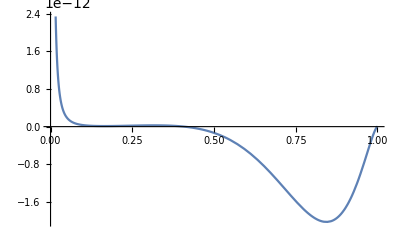

```mathematica
Plot[res3,{u,0,1}]
```